# Top

## Analysis

## Setup Packages

```mathematica
Needs["Ubuntu`Top`"];
```

```mathematica
Needs["Utilities`UnixTime`"];
```

```mathematica
Needs["Calendar`"];
```

```mathematica
Needs["Utilities`Debug`"]
```

http://linuxaria.com/howto/understanding-the-top-command-on-linux?lang=en

## Setup Data

```mathematica
dataDir=FileNameJoin[{ProjectDirectory["Ubuntu`Top`"],"TestData"}]
```

/Users/matt/WolframWorkspaces/Base2/Ubuntu/TestData

```mathematica
plotLabel="aws + ubuntu + node + haproxy + docker";
```

## TopDataFilePathQ

```mathematica
FileNames["top_*.txt",{dataDir}]
```

{/Users/matt/WolframWorkspaces/Base2/Ubuntu/TestData/top_1389986524.txt}

```mathematica
topDataFilePath=FileNames["top_*.txt",{dataDir}][[1]];
```

```mathematica
topDataFileTimestamp=TopDataFileTimestamp[topDataFilePath]
```

{2014,1,17,11,22,4.}

## TopLogFileData

```mathematica
topLogFileData=TopLogFileData[topDataFilePath];
```

```mathematica
TopLogFileDataQ[topLogFileData]//Timing
```

{0.00004,True}

```mathematica
FilePath[topLogFileData]
```

/Users/matt/WolframWorkspaces/Base2/Ubuntu/TestData/top_1389986524.txt

```mathematica
Table[Timing[Length[Lines[topLogFileData]]],{3}]//TableForm
```

438.60661 | 398
1.31501 | 398
0.00009 | 398

```mathematica
Map[TopDataQ,Lines[topLogFileData]]//Tally//Timing
```

{0.00543,{{True,398}}}

```mathematica
Table[Timing[Length[Map[TopSummary,Lines[topLogFileData]]]],{3}]//TableForm
```

2.05374 | 398
2.53957 | 398
2.64957 | 398

```mathematica
topSummaryList=Map[TopSummary,Lines[topLogFileData]];
```

```mathematica
topSummaryList[[1]]
```

[top data]:Wed 1 Jan 2014 11:22:04

```mathematica
Grid[Join[{{"Timestamp","Uptime","UserSessions","LoadAverage1Minute","LoadAverage5Minute","LoadAverage15Minute"}},Transpose[Map[Thread,Through[{Timestamp,Uptime,UserSessions,LoadAverage1Minute,LoadAverage5Minute,LoadAverage15Minute}[topSummaryList[[;;10]]]]]]/.{dateList:_?DateQ:>DateString[dateList],quantity_Quantity:>N[quantity]}],Alignment->{{Right,Left,Right,Right,Right,Right,Right},Automatic,{{1,1},{1,-1}}->Center},Dividers->{None,2->True},Frame->True,ItemSize->Full]
```

Timestamp | Uptime | UserSessions | LoadAverage1Minute | LoadAverage5Minute | LoadAverage15Minute
Wed 1 Jan 2014 11:22:04 | 8.84444 | 7 | 1.16 | 1.05 | 1.06
Wed 1 Jan 2014 11:22:07 | 8.84444 | 7 | 1.16 | 1.05 | 1.06
Wed 1 Jan 2014 11:22:11 | 8.84444 | 7 | 1.14 | 1.05 | 1.06
Wed 1 Jan 2014 11:22:14 | 8.84514 | 7 | 1.13 | 1.05 | 1.05
Wed 1 Jan 2014 11:22:17 | 8.84514 | 7 | 1.13 | 1.05 | 1.05
Wed 1 Jan 2014 11:22:20 | 8.84514 | 7 | 1.12 | 1.04 | 1.05
Wed 1 Jan 2014 11:22:23 | 8.84514 | 7 | 1.12 | 1.04 | 1.05
Wed 1 Jan 2014 11:22:26 | 8.84514 | 7 | 1.11 | 1.04 | 1.05
Wed 1 Jan 2014 11:22:29 | 8.84514 | 7 | 1.1 | 1.04 | 1.05
Wed 1 Jan 2014 11:22:32 | 8.84514 | 7 | 1.1 | 1.04 | 1.05

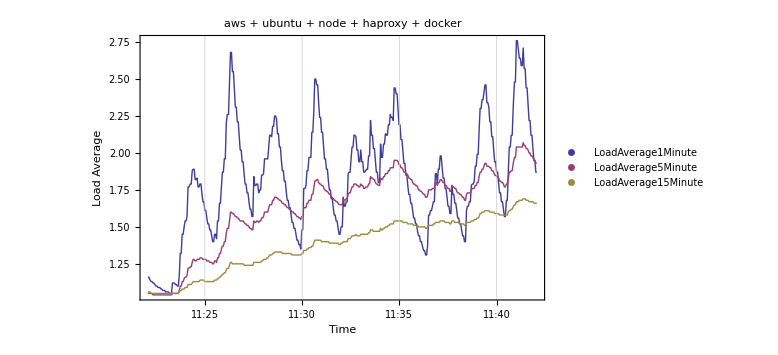

```mathematica
loadAveragePlot=LoadAveragePlot[topLogFileData,plotLabel]
```

```mathematica
Export[FileNameJoin[{$HomeDirectory,"Desktop",FileBaseName[topDataFilePath]<>"_loadAveragePlot"<>".png"}],loadAveragePlot]
```

/Users/matt/Desktop/top_1389986524_loadAveragePlot.png

```mathematica
Grid[Join[{{"Timestamp","TotalProcesses","TotalRunningProcesses","TotalSleepingProcesses","TotalStoppedProcesses","TotalZombieProcesses"}},Transpose[Map[Thread,Through[{Timestamp,TotalProcesses,TotalRunningProcesses,TotalSleepingProcesses,TotalStoppedProcesses,TotalZombieProcesses}[topSummaryList[[;;10]]]]]]/.{dateList:_?DateQ:>DateString[dateList]}],Alignment->{{Left,Right,Right,Right,Right,Right},Automatic,{{1,1},{1,-1}}->Center},Dividers->{None,2->True},Frame->True,ItemSize->Full]
```

Timestamp | TotalProcesses | TotalRunningProcesses | TotalSleepingProcesses | TotalStoppedProcesses | TotalZombieProcesses
Wed 1 Jan 2014 11:22:04 | 297 | 1 | 282 | 0 | 14
Wed 1 Jan 2014 11:22:07 | 297 | 1 | 282 | 0 | 14
Wed 1 Jan 2014 11:22:11 | 298 | 1 | 283 | 0 | 14
Wed 1 Jan 2014 11:22:14 | 302 | 1 | 287 | 0 | 14
Wed 1 Jan 2014 11:22:17 | 302 | 1 | 287 | 0 | 14
Wed 1 Jan 2014 11:22:20 | 303 | 1 | 288 | 0 | 14
Wed 1 Jan 2014 11:22:23 | 303 | 1 | 288 | 0 | 14
Wed 1 Jan 2014 11:22:26 | 303 | 1 | 288 | 0 | 14
Wed 1 Jan 2014 11:22:29 | 303 | 1 | 288 | 0 | 14
Wed 1 Jan 2014 11:22:32 | 303 | 1 | 288 | 0 | 14

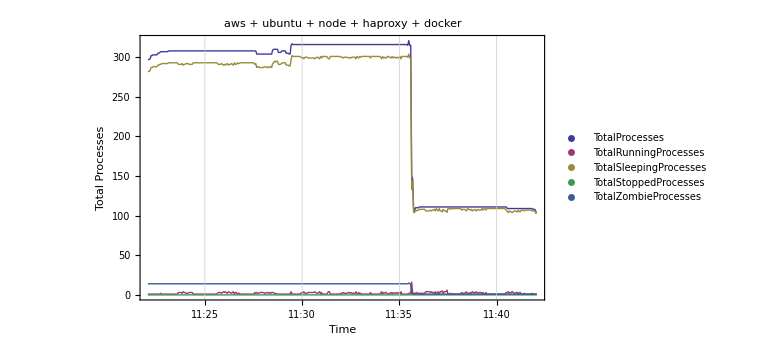

```mathematica
totalProcessesPlot=TotalProcessesPlot[topLogFileData,plotLabel]
```

```mathematica
Export[FileNameJoin[{$HomeDirectory,"Desktop",FileBaseName[topDataFilePath]<>"_totalProcessesPlot"<>".png"}],totalProcessesPlot]
```

/Users/matt/Desktop/top_1389986524_totalProcessesPlot.png

```mathematica
Grid[Join[{{"Timestamp","CPUPercentForUserProcesses","CPUPercentForSystemProcesses","CPUPercentWithPriorityUpgrade","CPUPercentNotUsed","CPUPercentForProcessesWaitingForIO","CPUPercentServingHardwareInterupts","CPUPercentServingSoftwareInterupts","CPUPercentStolenByHypervisor"}},Transpose[Map[Thread,Through[{Timestamp,CPUPercentForUserProcesses,CPUPercentForSystemProcesses,CPUPercentWithPriorityUpgrade,CPUPercentNotUsed,CPUPercentForProcessesWaitingForIO,CPUPercentServingHardwareInterupts,CPUPercentServingSoftwareInterupts,CPUPercentStolenByHypervisor}[topSummaryList[[;;10]]]]]]/.{dateList:_?DateQ:>DateString[dateList]}],Alignment->{{Left,Right,Right,Right,Right,Right,Right,Right,Right},Automatic,{{1,1},{1,-1}}->Center},Dividers->{None,2->True},Frame->True,ItemSize->Full]
```

Part::pspec: Part specification 2.3 is neither a machine-sized integer nor a list of machine-sized integers.

Part::pspec: Part specification 5.9 is neither a machine-sized integer nor a list of machine-sized integers.

Timestamp | CPUPercentForUserProcesses | CPUPercentForSystemProcesses | CPUPercentWithPriorityUpgrade | CPUPercentNotUsed | CPUPercentForProcessesWaitingForIO | CPUPercentServingHardwareInterupts | CPUPercentServingSoftwareInterupts | CPUPercentStolenByHypervisor
Wed 1 Jan 2014 11:22:04 | 0.3 | 0.2 | 0. | 99.4 | 0. | 0. | 0. | 0.
Wed 1 Jan 2014 11:22:07 | 0.2 | 0.5 | 0. | 99.3 | 0. | 0. | 0. | 0.
Wed 1 Jan 2014 11:22:11 | 0.3 | 0.5 | 0. | 99. | 0.2 | 0. | 0. | 0.
Wed 1 Jan 2014 11:22:14 | 2.3 | 1.5 | 0. | 96.2 | 0. | 0. | 0. | 0.
Wed 1 Jan 2014 11:22:17 | 5.9 | 6.6 | 0. | 81.2 | 6.3 | 0. | 0. | 0.
Wed 1 Jan 2014 11:22:20 | 0.3 | 1. | 0. | 98.7 | 0. | 0. | 0. | 0.
Wed 1 Jan 2014 11:22:23 | 0.5 | 0.8 | 0. | 97.7 | 1. | 0. | 0. | 0.
Wed 1 Jan 2014 11:22:26 | 0.3 | 1.2 | 0. | 98.5 | 0. | 0. | 0. | 0.
Wed 1 Jan 2014 11:22:29 | 0.5 | 0.5 | 0. | 99. | 0. | 0. | 0. | 0.
Wed 1 Jan 2014 11:22:32 | 0.3 | 0.5 | 0. | 99. | 0.2 | 0. | 0. | 0.

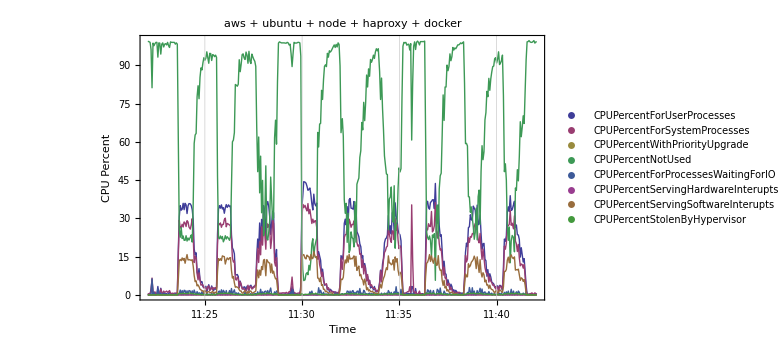

```mathematica
cpuPercentPlot=CPUPercentPlot[topLogFileData,plotLabel]
```

```mathematica
Export[FileNameJoin[{$HomeDirectory,"Desktop",FileBaseName[topDataFilePath]<>"_cpuPercentPlot"<>".png"}],cpuPercentPlot]
```

/Users/matt/Desktop/top_1389986524_cpuPercentPlot.png

```mathematica
Grid[Join[{{"Timestamp","TotalPhysicalMemory","UsedPhysicalMemory","FreePhysicalMemory","BufferPhysicalMemory"}},Transpose[Map[Thread,Through[{Timestamp,TotalPhysicalMemory,UsedPhysicalMemory,FreePhysicalMemory,BufferPhysicalMemory}[topSummaryList[[;;10]]]]]]/.{dateList:_?DateQ:>DateString[dateList]}],Alignment->{{Left,Right,Right,Right,Right},Automatic,{{1,1},{1,-1}}->Center},Dividers->{None,2->True},Frame->True,ItemSize->Full]
```

Timestamp | TotalPhysicalMemory | UsedPhysicalMemory | FreePhysicalMemory | BufferPhysicalMemory
Wed 1 Jan 2014 11:22:04 | 7629464 | 7590516 | 38948 | 767168
Wed 1 Jan 2014 11:22:07 | 7629464 | 7590640 | 38824 | 767168
Wed 1 Jan 2014 11:22:11 | 7629464 | 7590896 | 38568 | 767176
Wed 1 Jan 2014 11:22:14 | 7629464 | 7589612 | 39852 | 766980
Wed 1 Jan 2014 11:22:17 | 7629464 | 7589712 | 39752 | 766988
Wed 1 Jan 2014 11:22:20 | 7629464 | 7589992 | 39472 | 767004
Wed 1 Jan 2014 11:22:23 | 7629464 | 7590216 | 39248 | 767012
Wed 1 Jan 2014 11:22:26 | 7629464 | 7590364 | 39100 | 767020
Wed 1 Jan 2014 11:22:29 | 7629464 | 7590720 | 38744 | 767028
Wed 1 Jan 2014 11:22:32 | 7629464 | 7590712 | 38752 | 767036

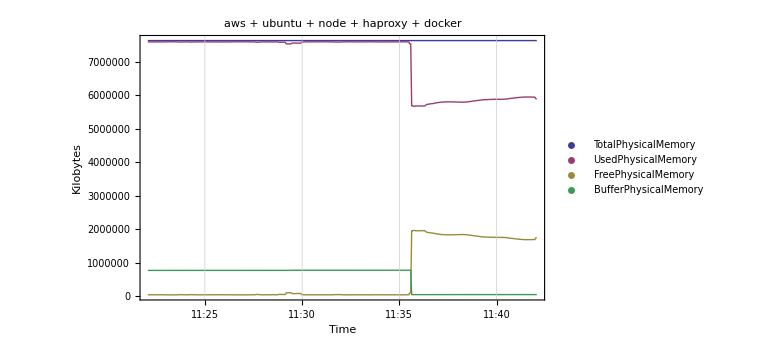

```mathematica
physicalMemoryPlot=PhysicalMemoryPlot[topLogFileData,plotLabel]
```

```mathematica
Export[FileNameJoin[{$HomeDirectory,"Desktop",FileBaseName[topDataFilePath]<>"_physicalMemoryPlot"<>".png"}],physicalMemoryPlot]
```

/Users/matt/Desktop/top_1389986524_physicalMemoryPlot.png

```mathematica
Grid[Join[{{"Timestamp","TotalSwapMemory","UsedSwapMemory","FreeSwapMemory","CachedSwapMemory"}},Transpose[Map[Thread,Through[{Timestamp,TotalSwapMemory,UsedSwapMemory,FreeSwapMemory,CachedSwapMemory}[topSummaryList[[;;10]]]]]]/.{dateList:_?DateQ:>DateString[dateList]}],Alignment->{{Left,Right,Right,Right,Right},Automatic,{{1,1},{1,-1}}->Center},Dividers->{None,2->True},Frame->True,ItemSize->Full]
```

Timestamp | TotalSwapMemory | UsedSwapMemory | FreeSwapMemory | CachedSwapMemory
Wed 1 Jan 2014 11:22:04 | 0 | 0 | 0 | 5497500
Wed 1 Jan 2014 11:22:07 | 0 | 0 | 0 | 5497564
Wed 1 Jan 2014 11:22:11 | 0 | 0 | 0 | 5497628
Wed 1 Jan 2014 11:22:14 | 0 | 0 | 0 | 5488588
Wed 1 Jan 2014 11:22:17 | 0 | 0 | 0 | 5484160
Wed 1 Jan 2014 11:22:20 | 0 | 0 | 0 | 5484296
Wed 1 Jan 2014 11:22:23 | 0 | 0 | 0 | 5484420
Wed 1 Jan 2014 11:22:26 | 0 | 0 | 0 | 5484560
Wed 1 Jan 2014 11:22:29 | 0 | 0 | 0 | 5484692
Wed 1 Jan 2014 11:22:32 | 0 | 0 | 0 | 5484820

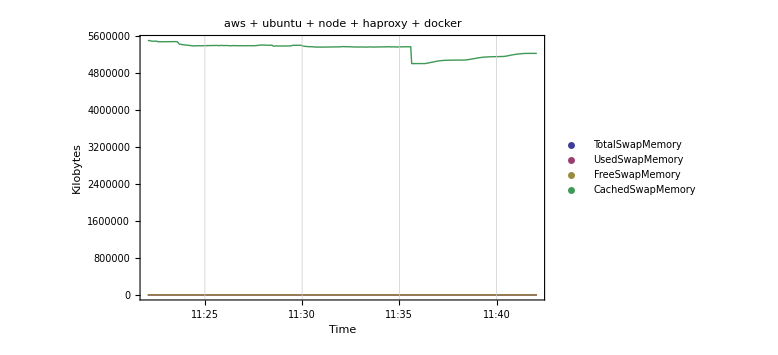

```mathematica
swapMemoryPlot=SwapMemoryPlot[topLogFileData,plotLabel]
```

```mathematica
Export[FileNameJoin[{$HomeDirectory,"Desktop",FileBaseName[topDataFilePath]<>"_swapMemoryPlot"<>".png"}],swapMemoryPlot]
```

/Users/matt/Desktop/top_1389986524_swapMemoryPlot.png

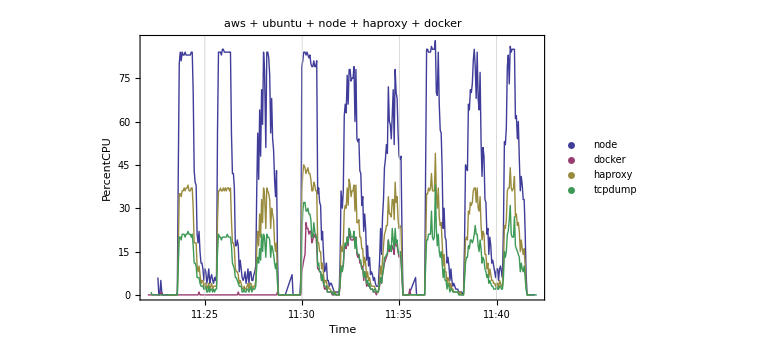

```mathematica
percentCPUPlot=CommandPlot[topLogFileData,plotLabel,{"node","docker","haproxy","tcpdump"},PercentCPU]
```

```mathematica
Export[FileNameJoin[{$HomeDirectory,"Desktop",FileBaseName[topDataFilePath]<>"_percentCPUPlot"<>".png"}],percentCPUPlot]
```

/Users/matt/Desktop/top_1389986524_percentCPUPlot.png

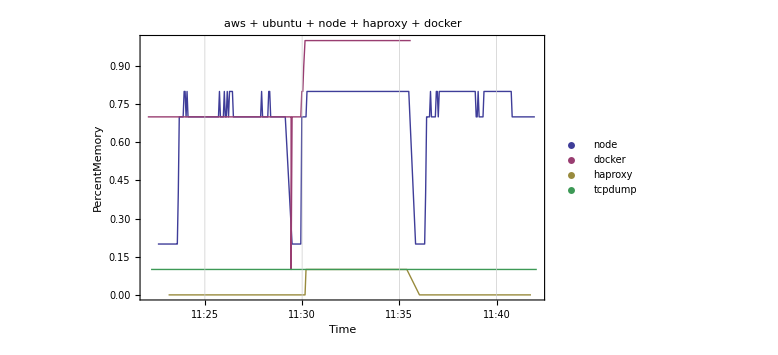

```mathematica
percentMemoryPlot=CommandPlot[topLogFileData,plotLabel,{"node","docker","haproxy","tcpdump"},PercentMemory]
```

```mathematica
Export[FileNameJoin[{$HomeDirectory,"Desktop",FileBaseName[topDataFilePath]<>"_percentMemoryPlot"<>".png"}],percentMemoryPlot]
```

/Users/matt/Desktop/top_1389986524_percentMemoryPlot.png

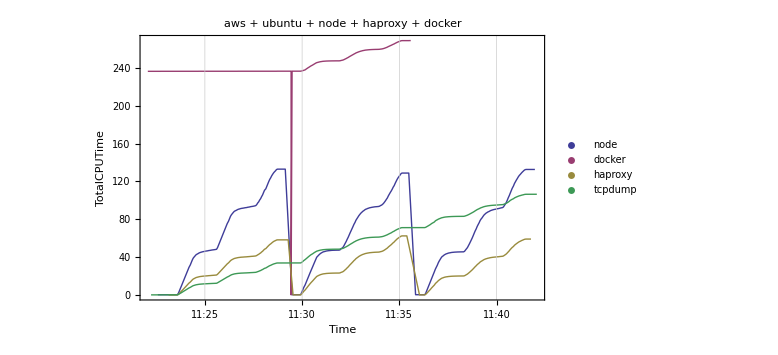

```mathematica
totalCPUTimePlot=CommandPlot[topLogFileData,plotLabel,{"node","docker","haproxy","tcpdump"},TotalCPUTime]
```

```mathematica
commandList={"node","docker","haproxy","tcpdump"};
```

```mathematica
pidList=Flatten[FindAllPIDForCommand[topLogFileData,#]&/@commandList,1][[All,2]]
```

{19643,19648,20051,20989,8550,20013,19684,20098,20997,19521}

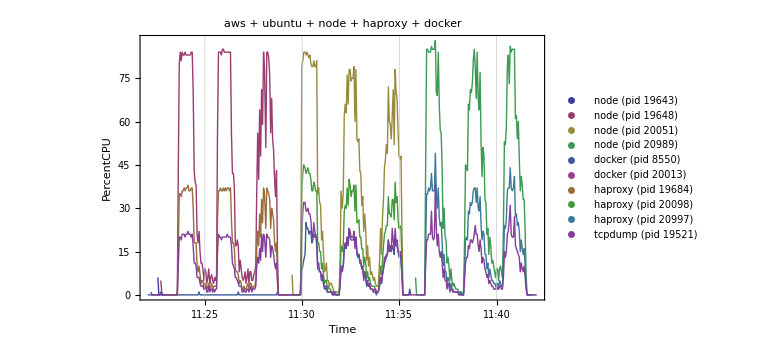

```mathematica
percentCPUPlot=PIDPlot[topLogFileData,plotLabel,pidList,PercentCPU]
```

```mathematica
Export[FileNameJoin[{$HomeDirectory,"Desktop",FileBaseName[topDataFilePath]<>"_percentCPUPlot"<>".png"}],percentCPUPlot]
```

/Users/matt/Desktop/top_1389986524_percentCPUPlot.png

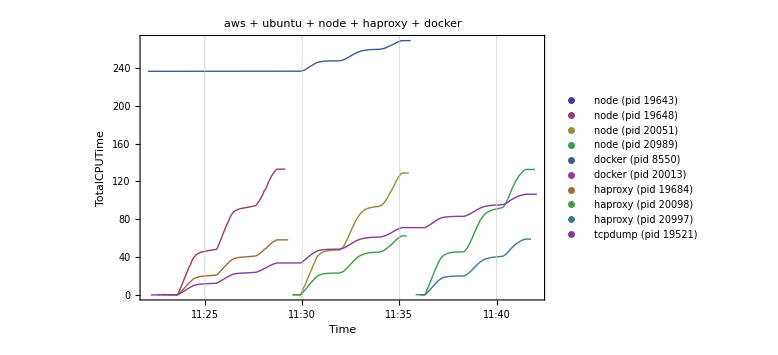

```mathematica
totalCPUTimePlot=PIDPlot[topLogFileData,plotLabel,pidList,TotalCPUTime]
```

```mathematica
Export[FileNameJoin[{$HomeDirectory,"Desktop",FileBaseName[topDataFilePath]<>"_totalCPUTimePlot"<>".png"}],totalCPUTimePlot]
```

/Users/matt/Desktop/top_1389986524_totalCPUTimePlot.png

```mathematica
Reverse[SortBy[Flatten[Map[ProcessListItemList,Lines[topLogFileData]]],PercentCPU]][[;;10]]//TableForm
```

[top data]:20989 ubuntu    20   0  657m  55m 5700 R   88  0.7   0:27.20 node                                                                                                                                               
[top data]:20989 ubuntu    20   0  657m  56m 5700 R   86  0.8   1:47.64 node                                                                                                                                               
[top data]:20989 ubuntu    20   0  656m  54m 5700 R   86  0.7   0:16.88 node                                                                                                                                               
[top data]:20989 ubuntu    20   0  658m  57m 5700 R   85  0.8   1:05.43 node                                                                                                                                               
[top data]:20989 ubuntu    20   0  657m  54m 5700 R   85  0.7   0:04.08 node                                                                                                                                               
[top data]:20989 ubuntu    20   0  656m  55m 5700 R   85  0.7   1:57.84 node                                                                                                                                               
[top data]:20989 ubuntu    20   0  656m  54m 5700 R   85  0.7   1:55.28 node                                                                                                                                               
[top data]:20989 ubuntu    20   0  656m  54m 5700 R   85  0.7   0:06.64 node                                                                                                                                               
[top data]:20989 ubuntu    20   0  656m  53m 5700 R   85  0.7   0:19.43 node                                                                                                                                               
[top data]:20989 ubuntu    20   0  655m  54m 5700 R   85  0.7   0:24.54 node

```mathematica
Reverse[SortBy[Select[Flatten[Map[ProcessListItemList,Lines[topLogFileData]]],!MemberQ[{"node","docker","haproxy","tcpdump","top"},Command[#]]&],PercentCPU]][[;;10]]//TableForm
```

[top data]:19900 ubuntu    20   0 25824 8192 1628 S   16  0.1   0:00.49 bash                                                                                                                                               
[top data]:19742 ubuntu    20   0 23364 5792 1620 S   14  0.1   0:00.41 bash                                                                                                                                               
[top data]:19522 ubuntu    20   0 25856 8224 1620 S   14  0.1   0:00.50 bash                                                                                                                                               
[top data]:20988 ubuntu    20   0 14312  892  732 S    7  0.0   0:08.59 logger                                                                                                                                             
[top data]:20988 ubuntu    20   0 14312  892  732 S    7  0.0   0:07.85 logger                                                                                                                                             
[top data]:20988 ubuntu    20   0 14312  892  732 S    7  0.0   0:01.93 logger                                                                                                                                             
[top data]:20988 ubuntu    20   0 14312  892  732 S    7  0.0   0:01.17 logger                                                                                                                                             
[top data]:20988 ubuntu    20   0 14312  892  732 S    6  0.0   0:08.39 logger                                                                                                                                             
[top data]:20988 ubuntu    20   0 14312  892  732 S    6  0.0   0:08.04 logger                                                                                                                                             
[top data]:20988 ubuntu    20   0 14312  892  732 S    6  0.0   0:07.65 logger

```mathematica
Grid[Join[{{"LineNumber","Timestamp","PID","User","Priority","Nice","VirtualMemory","PhysicalMemory","SharedMemory","Status","PercentCPU","PercentMemory","TotalCPUTime","Command"}},Transpose[Map[Thread,Through[{LineNumber,Timestamp,PID,User,Priority,Nice,VirtualMemory,PhysicalMemory,SharedMemory,Status,PercentCPU,PercentMemory,TotalCPUTime,Command}[FindProcessByCommand[topLogFileData,"docker"]]]]]/.{dateList:_?DateQ:>DateString[dateList],quantity_Quantity:>N[quantity]}],Alignment->{{Right,Left,Right,Left,Right,Right,Right,Right,Right,Center,Right,Right,Right,Left},Automatic,{{1,1},{1,-1}}->Center},Dividers->{None,2->True},Frame->True,ItemSize->Full]
```

LineNumber | Timestamp | PID | User | Priority | Nice | VirtualMemory | PhysicalMemory | SharedMemory | Status | PercentCPU | PercentMemory | TotalCPUTime | Command
67 | Wed 1 Jan 2014 11:22:04 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.58 | docker
373 | Wed 1 Jan 2014 11:22:07 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.58 | docker
679 | Wed 1 Jan 2014 11:22:11 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.58 | docker
990 | Wed 1 Jan 2014 11:22:14 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.58 | docker
1298 | Wed 1 Jan 2014 11:22:17 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.58 | docker
1608 | Wed 1 Jan 2014 11:22:20 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.58 | docker
1921 | Wed 1 Jan 2014 11:22:23 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.58 | docker
2234 | Wed 1 Jan 2014 11:22:26 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.58 | docker
2545 | Wed 1 Jan 2014 11:22:29 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.58 | docker
2856 | Wed 1 Jan 2014 11:22:32 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.58 | docker
3171 | Wed 1 Jan 2014 11:22:35 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.58 | docker
3482 | Wed 1 Jan 2014 11:22:38 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.58 | docker
3798 | Wed 1 Jan 2014 11:22:41 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.58 | docker
4053 | Wed 1 Jan 2014 11:22:44 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 1 | 0.7 | 236.61 | docker
4432 | Wed 1 Jan 2014 11:22:47 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.61 | docker
4746 | Wed 1 Jan 2014 11:22:50 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.61 | docker
5062 | Wed 1 Jan 2014 11:22:53 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.61 | docker
5377 | Wed 1 Jan 2014 11:22:56 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.61 | docker
5693 | Wed 1 Jan 2014 11:22:59 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.61 | docker
6009 | Wed 1 Jan 2014 11:23:02 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.61 | docker
6325 | Wed 1 Jan 2014 11:23:05 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.61 | docker
6643 | Wed 1 Jan 2014 11:23:08 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.61 | docker
6960 | Wed 1 Jan 2014 11:23:11 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.61 | docker
7274 | Wed 1 Jan 2014 11:23:14 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.61 | docker
7591 | Wed 1 Jan 2014 11:23:17 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.61 | docker
7908 | Wed 1 Jan 2014 11:23:20 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.61 | docker
8227 | Wed 1 Jan 2014 11:23:23 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.61 | docker
8543 | Wed 1 Jan 2014 11:23:26 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.61 | docker
8859 | Wed 1 Jan 2014 11:23:29 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.61 | docker
9176 | Wed 1 Jan 2014 11:23:32 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.61 | docker
9496 | Wed 1 Jan 2014 11:23:35 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.61 | docker
9815 | Wed 1 Jan 2014 11:23:38 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.61 | docker
10131 | Wed 1 Jan 2014 11:23:41 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.61 | docker
10391 | Wed 1 Jan 2014 11:23:44 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.62 | docker
10768 | Wed 1 Jan 2014 11:23:47 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.62 | docker
11083 | Wed 1 Jan 2014 11:23:50 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.62 | docker
11400 | Wed 1 Jan 2014 11:23:53 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.62 | docker
11717 | Wed 1 Jan 2014 11:23:56 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.62 | docker
12034 | Wed 1 Jan 2014 11:23:59 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.62 | docker
12350 | Wed 1 Jan 2014 11:24:02 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.62 | docker
12668 | Wed 1 Jan 2014 11:24:05 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.62 | docker
12984 | Wed 1 Jan 2014 11:24:08 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.62 | docker
13303 | Wed 1 Jan 2014 11:24:11 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.62 | docker
13618 | Wed 1 Jan 2014 11:24:15 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.62 | docker
13936 | Wed 1 Jan 2014 11:24:18 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.62 | docker
14252 | Wed 1 Jan 2014 11:24:21 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.62 | docker
14571 | Wed 1 Jan 2014 11:24:24 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.62 | docker
14888 | Wed 1 Jan 2014 11:24:27 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.62 | docker
15202 | Wed 1 Jan 2014 11:24:30 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.62 | docker
15520 | Wed 1 Jan 2014 11:24:33 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.62 | docker
15838 | Wed 1 Jan 2014 11:24:36 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.62 | docker
16155 | Wed 1 Jan 2014 11:24:39 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.62 | docker
16412 | Wed 1 Jan 2014 11:24:42 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 1 | 0.7 | 236.65 | docker
16788 | Wed 1 Jan 2014 11:24:45 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
17107 | Wed 1 Jan 2014 11:24:48 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
17424 | Wed 1 Jan 2014 11:24:51 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
17738 | Wed 1 Jan 2014 11:24:54 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
18056 | Wed 1 Jan 2014 11:24:57 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
18372 | Wed 1 Jan 2014 11:25:00 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
18691 | Wed 1 Jan 2014 11:25:03 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
19008 | Wed 1 Jan 2014 11:25:06 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
19324 | Wed 1 Jan 2014 11:25:09 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
19641 | Wed 1 Jan 2014 11:25:12 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
19959 | Wed 1 Jan 2014 11:25:15 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
20276 | Wed 1 Jan 2014 11:25:18 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
20591 | Wed 1 Jan 2014 11:25:21 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
20910 | Wed 1 Jan 2014 11:25:24 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
21226 | Wed 1 Jan 2014 11:25:27 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
21544 | Wed 1 Jan 2014 11:25:30 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
21860 | Wed 1 Jan 2014 11:25:33 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
22179 | Wed 1 Jan 2014 11:25:36 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
22494 | Wed 1 Jan 2014 11:25:39 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
22812 | Wed 1 Jan 2014 11:25:42 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
23129 | Wed 1 Jan 2014 11:25:45 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
23447 | Wed 1 Jan 2014 11:25:48 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
23764 | Wed 1 Jan 2014 11:25:51 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
24080 | Wed 1 Jan 2014 11:25:54 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
24395 | Wed 1 Jan 2014 11:25:57 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
24713 | Wed 1 Jan 2014 11:26:00 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
25031 | Wed 1 Jan 2014 11:26:03 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
25347 | Wed 1 Jan 2014 11:26:06 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
25665 | Wed 1 Jan 2014 11:26:09 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
25982 | Wed 1 Jan 2014 11:26:13 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
26302 | Wed 1 Jan 2014 11:26:16 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
26615 | Wed 1 Jan 2014 11:26:19 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
26932 | Wed 1 Jan 2014 11:26:22 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
27250 | Wed 1 Jan 2014 11:26:25 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
27567 | Wed 1 Jan 2014 11:26:28 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
27883 | Wed 1 Jan 2014 11:26:31 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
28201 | Wed 1 Jan 2014 11:26:34 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
28518 | Wed 1 Jan 2014 11:26:37 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
28836 | Wed 1 Jan 2014 11:26:40 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.65 | docker
29092 | Wed 1 Jan 2014 11:26:43 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 1 | 0.7 | 236.68 | docker
29468 | Wed 1 Jan 2014 11:26:46 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
29785 | Wed 1 Jan 2014 11:26:49 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
30103 | Wed 1 Jan 2014 11:26:52 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
30419 | Wed 1 Jan 2014 11:26:55 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
30737 | Wed 1 Jan 2014 11:26:58 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
31056 | Wed 1 Jan 2014 11:27:01 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
31370 | Wed 1 Jan 2014 11:27:04 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
31689 | Wed 1 Jan 2014 11:27:07 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
32004 | Wed 1 Jan 2014 11:27:10 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
32321 | Wed 1 Jan 2014 11:27:13 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
32639 | Wed 1 Jan 2014 11:27:16 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
32955 | Wed 1 Jan 2014 11:27:19 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
33273 | Wed 1 Jan 2014 11:27:22 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
33590 | Wed 1 Jan 2014 11:27:25 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
33906 | Wed 1 Jan 2014 11:27:28 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
34225 | Wed 1 Jan 2014 11:27:31 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
34540 | Wed 1 Jan 2014 11:27:34 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
34858 | Wed 1 Jan 2014 11:27:37 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
35175 | Wed 1 Jan 2014 11:27:40 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
35487 | Wed 1 Jan 2014 11:27:43 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
35801 | Wed 1 Jan 2014 11:27:46 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
36116 | Wed 1 Jan 2014 11:27:49 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
36426 | Wed 1 Jan 2014 11:27:52 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
36740 | Wed 1 Jan 2014 11:27:55 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
37054 | Wed 1 Jan 2014 11:27:58 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
37365 | Wed 1 Jan 2014 11:28:01 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
37679 | Wed 1 Jan 2014 11:28:04 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
37992 | Wed 1 Jan 2014 11:28:08 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
38305 | Wed 1 Jan 2014 11:28:11 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
38617 | Wed 1 Jan 2014 11:28:14 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
38930 | Wed 1 Jan 2014 11:28:17 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
39243 | Wed 1 Jan 2014 11:28:20 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
39558 | Wed 1 Jan 2014 11:28:23 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
39869 | Wed 1 Jan 2014 11:28:26 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
40187 | Wed 1 Jan 2014 11:28:29 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
40503 | Wed 1 Jan 2014 11:28:32 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
40819 | Wed 1 Jan 2014 11:28:35 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
41139 | Wed 1 Jan 2014 11:28:38 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
41458 | Wed 1 Jan 2014 11:28:41 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.68 | docker
41715 | Wed 1 Jan 2014 11:28:44 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 1 | 0.7 | 236.72 | docker
42092 | Wed 1 Jan 2014 11:28:47 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.72 | docker
42408 | Wed 1 Jan 2014 11:28:50 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.72 | docker
42723 | Wed 1 Jan 2014 11:28:53 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.72 | docker
43038 | Wed 1 Jan 2014 11:28:56 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.72 | docker
43354 | Wed 1 Jan 2014 11:28:59 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.72 | docker
43670 | Wed 1 Jan 2014 11:29:02 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.72 | docker
43987 | Wed 1 Jan 2014 11:29:05 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.72 | docker
44303 | Wed 1 Jan 2014 11:29:08 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.72 | docker
44621 | Wed 1 Jan 2014 11:29:11 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.72 | docker
44936 | Wed 1 Jan 2014 11:29:14 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.72 | docker
45251 | Wed 1 Jan 2014 11:29:17 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.72 | docker
45563 | Wed 1 Jan 2014 11:29:20 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.72 | docker
45879 | Wed 1 Jan 2014 11:29:23 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.72 | docker
46134 | Wed 1 Jan 2014 11:29:26 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.73 | docker
46139 | Wed 1 Jan 2014 11:29:26 | 20013 | root | 20 | 0 | 1.76×10^8 | 4068. | 3212. | S | 0 | 0.1 | 0.01 | docker
46516 | Wed 1 Jan 2014 11:29:29 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.73 | docker
46841 | Wed 1 Jan 2014 11:29:32 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.73 | docker
47164 | Wed 1 Jan 2014 11:29:35 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.73 | docker
47490 | Wed 1 Jan 2014 11:29:38 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.73 | docker
47814 | Wed 1 Jan 2014 11:29:41 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.73 | docker
48139 | Wed 1 Jan 2014 11:29:44 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.73 | docker
48465 | Wed 1 Jan 2014 11:29:47 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.73 | docker
48787 | Wed 1 Jan 2014 11:29:50 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.73 | docker
49115 | Wed 1 Jan 2014 11:29:53 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.73 | docker
49384 | Wed 1 Jan 2014 11:29:56 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.5×10^7 | 6224. | S | 0 | 0.7 | 236.74 | docker
49706 | Wed 1 Jan 2014 11:29:59 | 8550 | root | 20 | 0 | 1.314×10^9 | 5.7×10^7 | 6224. | S | 8 | 0.8 | 236.98 | docker
50031 | Wed 1 Jan 2014 11:30:02 | 8550 | root | 20 | 0 | 1.314×10^9 | 6.2×10^7 | 6224. | S | 10 | 0.8 | 237.28 | docker
50356 | Wed 1 Jan 2014 11:30:05 | 8550 | root | 20 | 0 | 1.314×10^9 | 6.8×10^7 | 6224. | S | 12 | 0.9 | 237.65 | docker
50681 | Wed 1 Jan 2014 11:30:09 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.4×10^7 | 6224. | S | 14 | 1. | 238.08 | docker
51006 | Wed 1 Jan 2014 11:30:12 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.6×10^7 | 6224. | S | 25 | 1. | 238.84 | docker
51331 | Wed 1 Jan 2014 11:30:15 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.6×10^7 | 6224. | S | 23 | 1. | 239.55 | docker
51656 | Wed 1 Jan 2014 11:30:18 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.6×10^7 | 6224. | S | 23 | 1. | 240.25 | docker
51981 | Wed 1 Jan 2014 11:30:21 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.6×10^7 | 6224. | S | 21 | 1. | 240.89 | docker
52306 | Wed 1 Jan 2014 11:30:24 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.6×10^7 | 6224. | S | 22 | 1. | 241.57 | docker
52631 | Wed 1 Jan 2014 11:30:27 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 22 | 1. | 242.24 | docker
52956 | Wed 1 Jan 2014 11:30:30 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 18 | 1. | 242.78 | docker
53281 | Wed 1 Jan 2014 11:30:33 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 19 | 1. | 243.35 | docker
53606 | Wed 1 Jan 2014 11:30:36 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 21 | 1. | 243.99 | docker
53931 | Wed 1 Jan 2014 11:30:39 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 20 | 1. | 244.6 | docker
54255 | Wed 1 Jan 2014 11:30:42 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 21 | 1. | 245.24 | docker
54581 | Wed 1 Jan 2014 11:30:45 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 17 | 1. | 245.74 | docker
54906 | Wed 1 Jan 2014 11:30:48 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 9 | 1. | 246.02 | docker
55231 | Wed 1 Jan 2014 11:30:51 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 9 | 1. | 246.3 | docker
55555 | Wed 1 Jan 2014 11:30:54 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 8 | 1. | 246.55 | docker
55881 | Wed 1 Jan 2014 11:30:57 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 8 | 1. | 246.79 | docker
56206 | Wed 1 Jan 2014 11:31:00 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 5 | 1. | 246.93 | docker
56531 | Wed 1 Jan 2014 11:31:03 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 6 | 1. | 247.11 | docker
56855 | Wed 1 Jan 2014 11:31:06 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 4 | 1. | 247.23 | docker
57181 | Wed 1 Jan 2014 11:31:09 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 2 | 1. | 247.3 | docker
57506 | Wed 1 Jan 2014 11:31:12 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 2 | 1. | 247.37 | docker
57831 | Wed 1 Jan 2014 11:31:15 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 3 | 1. | 247.45 | docker
58155 | Wed 1 Jan 2014 11:31:18 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 1 | 1. | 247.48 | docker
58480 | Wed 1 Jan 2014 11:31:21 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 1 | 1. | 247.52 | docker
58806 | Wed 1 Jan 2014 11:31:24 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 1 | 1. | 247.55 | docker
59131 | Wed 1 Jan 2014 11:31:27 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 1 | 1. | 247.57 | docker
59455 | Wed 1 Jan 2014 11:31:30 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 1 | 1. | 247.6 | docker
59784 | Wed 1 Jan 2014 11:31:33 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 0 | 1. | 247.61 | docker
60108 | Wed 1 Jan 2014 11:31:36 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 0 | 1. | 247.62 | docker
60432 | Wed 1 Jan 2014 11:31:39 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 0 | 1. | 247.63 | docker
60756 | Wed 1 Jan 2014 11:31:42 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 1 | 1. | 247.65 | docker
61082 | Wed 1 Jan 2014 11:31:45 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 0 | 1. | 247.66 | docker
61466 | Wed 1 Jan 2014 11:31:48 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 0 | 1. | 247.66 | docker
61793 | Wed 1 Jan 2014 11:31:51 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 0 | 1. | 247.66 | docker
62116 | Wed 1 Jan 2014 11:31:54 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 0 | 1. | 247.66 | docker
62381 | Wed 1 Jan 2014 11:31:57 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 3 | 1. | 247.76 | docker
62706 | Wed 1 Jan 2014 11:32:00 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 9 | 1. | 248.03 | docker
63030 | Wed 1 Jan 2014 11:32:04 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 10 | 1. | 248.34 | docker
63356 | Wed 1 Jan 2014 11:32:07 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 10 | 1. | 248.63 | docker
63681 | Wed 1 Jan 2014 11:32:10 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 16 | 1. | 249.11 | docker
64006 | Wed 1 Jan 2014 11:32:13 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 17 | 1. | 249.63 | docker
64331 | Wed 1 Jan 2014 11:32:16 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 16 | 1. | 250.12 | docker
64656 | Wed 1 Jan 2014 11:32:19 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 20 | 1. | 250.72 | docker
64981 | Wed 1 Jan 2014 11:32:22 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 17 | 1. | 251.23 | docker
65306 | Wed 1 Jan 2014 11:32:25 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 23 | 1. | 251.92 | docker
65631 | Wed 1 Jan 2014 11:32:28 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 20 | 1. | 252.52 | docker
65956 | Wed 1 Jan 2014 11:32:31 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 19 | 1. | 253.09 | docker
66281 | Wed 1 Jan 2014 11:32:34 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 19 | 1. | 253.68 | docker
66606 | Wed 1 Jan 2014 11:32:37 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 19 | 1. | 254.25 | docker
66931 | Wed 1 Jan 2014 11:32:40 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 20 | 1. | 254.85 | docker
67255 | Wed 1 Jan 2014 11:32:43 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 18 | 1. | 255.39 | docker
67581 | Wed 1 Jan 2014 11:32:46 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 20 | 1. | 256. | docker
67906 | Wed 1 Jan 2014 11:32:49 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 14 | 1. | 256.43 | docker
68231 | Wed 1 Jan 2014 11:32:52 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 13 | 1. | 256.83 | docker
68556 | Wed 1 Jan 2014 11:32:55 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 14 | 1. | 257.25 | docker
68881 | Wed 1 Jan 2014 11:32:58 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 11 | 1. | 257.58 | docker
69206 | Wed 1 Jan 2014 11:33:01 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 11 | 1. | 257.91 | docker
69531 | Wed 1 Jan 2014 11:33:04 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 9 | 1. | 258.17 | docker
69855 | Wed 1 Jan 2014 11:33:07 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 10 | 1. | 258.48 | docker
70181 | Wed 1 Jan 2014 11:33:10 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 5 | 1. | 258.64 | docker
70505 | Wed 1 Jan 2014 11:33:13 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 8 | 1. | 258.87 | docker
70830 | Wed 1 Jan 2014 11:33:16 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 6 | 1. | 259.05 | docker
71156 | Wed 1 Jan 2014 11:33:19 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 3 | 1. | 259.15 | docker
71481 | Wed 1 Jan 2014 11:33:22 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 4 | 1. | 259.27 | docker
71805 | Wed 1 Jan 2014 11:33:25 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 3 | 1. | 259.37 | docker
72131 | Wed 1 Jan 2014 11:33:28 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 3 | 1. | 259.47 | docker
72456 | Wed 1 Jan 2014 11:33:31 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 2 | 1. | 259.53 | docker
72781 | Wed 1 Jan 2014 11:33:34 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 2 | 1. | 259.59 | docker
73106 | Wed 1 Jan 2014 11:33:37 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 2 | 1. | 259.64 | docker
73430 | Wed 1 Jan 2014 11:33:40 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 1 | 1. | 259.68 | docker
73756 | Wed 1 Jan 2014 11:33:43 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 1 | 1. | 259.72 | docker
74081 | Wed 1 Jan 2014 11:33:46 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 1 | 1. | 259.76 | docker
74409 | Wed 1 Jan 2014 11:33:49 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 0 | 1. | 259.77 | docker
74730 | Wed 1 Jan 2014 11:33:52 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 1 | 1. | 259.8 | docker
75056 | Wed 1 Jan 2014 11:33:55 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 1 | 1. | 259.82 | docker
75381 | Wed 1 Jan 2014 11:33:59 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 3 | 1. | 259.91 | docker
75706 | Wed 1 Jan 2014 11:34:02 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 6 | 1. | 260.08 | docker
76031 | Wed 1 Jan 2014 11:34:05 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 4 | 1. | 260.19 | docker
76355 | Wed 1 Jan 2014 11:34:08 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 7 | 1. | 260.4 | docker
76681 | Wed 1 Jan 2014 11:34:11 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 9 | 1. | 260.66 | docker
77006 | Wed 1 Jan 2014 11:34:14 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 11 | 1. | 261. | docker
77331 | Wed 1 Jan 2014 11:34:17 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 12 | 1. | 261.37 | docker
77656 | Wed 1 Jan 2014 11:34:20 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 13 | 1. | 261.77 | docker
77980 | Wed 1 Jan 2014 11:34:23 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 14 | 1. | 262.2 | docker
78306 | Wed 1 Jan 2014 11:34:26 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 19 | 1. | 262.76 | docker
78631 | Wed 1 Jan 2014 11:34:29 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 15 | 1. | 263.21 | docker
78956 | Wed 1 Jan 2014 11:34:32 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 16 | 1. | 263.71 | docker
79281 | Wed 1 Jan 2014 11:34:35 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 15 | 1. | 264.15 | docker
79606 | Wed 1 Jan 2014 11:34:38 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 17 | 1. | 264.67 | docker
79931 | Wed 1 Jan 2014 11:34:41 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 16 | 1. | 265.16 | docker
80256 | Wed 1 Jan 2014 11:34:44 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 14 | 1. | 265.6 | docker
80581 | Wed 1 Jan 2014 11:34:47 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 20 | 1. | 266.2 | docker
80906 | Wed 1 Jan 2014 11:34:50 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 17 | 1. | 266.7 | docker
81231 | Wed 1 Jan 2014 11:34:53 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 17 | 1. | 267.23 | docker
81555 | Wed 1 Jan 2014 11:34:56 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 15 | 1. | 267.68 | docker
81881 | Wed 1 Jan 2014 11:34:59 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 13 | 1. | 268.07 | docker
82205 | Wed 1 Jan 2014 11:35:02 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 15 | 1. | 268.52 | docker
82531 | Wed 1 Jan 2014 11:35:05 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 12 | 1. | 268.87 | docker
82856 | Wed 1 Jan 2014 11:35:08 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 6 | 1. | 269.05 | docker
83239 | Wed 1 Jan 2014 11:35:11 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 0 | 1. | 269.05 | docker
83563 | Wed 1 Jan 2014 11:35:14 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 0 | 1. | 269.05 | docker
83890 | Wed 1 Jan 2014 11:35:17 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 0 | 1. | 269.05 | docker
84214 | Wed 1 Jan 2014 11:35:20 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 0 | 1. | 269.05 | docker
84542 | Wed 1 Jan 2014 11:35:23 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 0 | 1. | 269.05 | docker
84863 | Wed 1 Jan 2014 11:35:26 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 0 | 1. | 269.05 | docker
85190 | Wed 1 Jan 2014 11:35:29 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.7×10^7 | 6224. | S | 0 | 1. | 269.05 | docker
85457 | Wed 1 Jan 2014 11:35:32 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.8×10^7 | 6224. | S | 2 | 1. | 269.1 | docker
85841 | Wed 1 Jan 2014 11:35:35 | 8550 | root | 20 | 0 | 1.314×10^9 | 7.8×10^7 | 6224. | S | 0 | 1. | 269.1 | docker